### Settings

```mathematica
dx = 4.58/0.529;
dy = 6.48/0.529;
a=132.7/0.529;
delta =0.0001;
rMaxX=100; 
rMaxY=50; 
Z =0.095; 
m = 0.075;
coord = {{0,0},{-dx,0},{dx,0},{-2*dx,0},{2*dx,0},{-3*dx,0},{3*dx,0}};
```

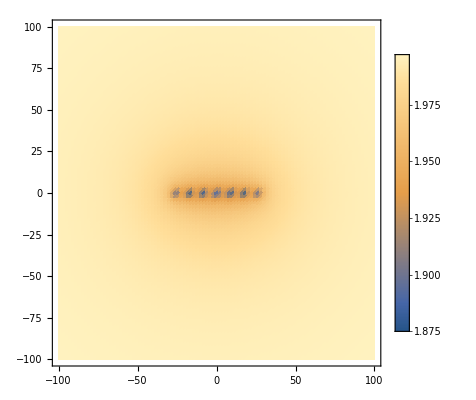

```mathematica
V[x_, y_] := Sum[(-Z)/(Sqrt[(x- coord[[i]][[1]])^2  + (y-coord[[i]][[2]])^2]+delta)*Exp[-Sqrt[(x-coord[[i]][[1]])^2  + (y-coord[[i]][[2]])^2]/a] ,{i,7} ] +2  ;
DensityPlot[V[x ,y],{x,-rMaxX,rMaxX},{y,-rMaxY,rMaxY}, (*PlotTheme->"Minimal",*) PlotPoints->100,  PlotLegends->Automatic, PlotRange->All]
Export[NotebookDirectory[]<>"Coulomb.png",%,ImageResolution->100];
```

```mathematica
|
```

### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/(2*m))* Laplacian[R2D[x,y],{x,y},"Cartesian"]+V[x,y]*R2D[x,y]
,DirichletCondition[R2D[x,y]==0,x==-rMaxX || x==rMaxX || y==-rMaxY || y==rMaxY]},
R2D[x,y],{x,-rMaxX,rMaxX},{y,-rMaxY,rMaxY},8, Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->1000000}(* "Direct"*),"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}  ];
ord =Ordering[egnVal];
Sort[Re[egnVal]]
```

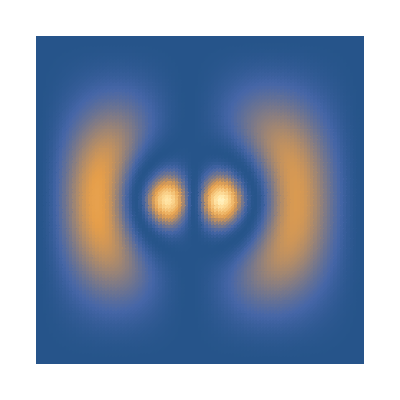

```mathematica
F1 =Part[Re[egnVec],Part[ord,7]]^2;
DensityPlot[F1,{x,-rMaxX,rMaxX},{y,-rMaxY,rMaxY}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All  (*PlotLegends->Automatic*)]
```